```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*File Names*)
FileNames["*.xls"]
FileNames["*.txt"]
```

{基准组 5 10 10.xls,FormicAcid100.xls,FormicAcid125.xls,FormicAcid25.xls,FormicAcid75.xls,HCl10.xls,HCl4.xls,HCl6.xls,HCl8.xls,KBr15.xls,KBr20.xls,KBr5.xls,KBr75.xls,TEM30.xls,TEM35.xls,TEM40.xls,TEM45.xls}

{10_4HCL.txt,10_HCL-5.txt,10_HCL-6.txt,10_HCL-8.txt,10_KBR-10.txt,10_KBR-15.txt,10_KBR-20.txt,10_KBR-5.txt,10_KBR-6.txt,11_FAcid10.txt,11_FAcid25.txt,11_FAcid35.txt,11_FAcid5.txt,11_FAcid75.txt,11_Temp30.txt,11_Temp35.txt,11_Temp40.txt,11_Temp45.txt,HCL-10.txt}

```mathematica
(*Constants*)
h=6.626070040*10^-34;
NA=6.022140857*10^23;
c=299792458;
k=1.38064852×10^-23;
R=NA k;
e=1.6021766208*^-19;
F=e*NA;
```

```mathematica
(*Functions*)
<<MaTeX`
TimesNewRoman[string_]:=Style[string,"Times New Roman",12,Black];
GraphFormatize[object_,otheroption___]:=Show[object,Frame->True,Axes->False,FrameTicksStyle->Directive[12,Black,"Times New Roman"],FrameStyle->Thickness[0.003],PlotStyle->Black,otheroption];
RangeSelect={{25,317},{38,360},{57,311},{147,311},{30,262},{18,296},{37,425},{16,274},{33,388},{504,725},{692,1863},{266,551},{404,667},{455,767},{156,466},{261,474},{233,398},{69,195},{17,309}};
thermalrangeselectedlist=(#-#[[1]])/1000&/@MapThread[Take][{First/@Import[#,"Table"]&/@FileNames["*.txt"],RangeSelect}];
SlopeExtractor[dataset_]:=Last/@(#["BestFitParameters"]&/@dataset);
```

```mathematica
(*Data from Caliberation*)
temprawlist=FileNames["*.xls"][[{1,-4,-3,-2,-1}]];
hclrawlist=FileNames["*.xls"][[{7,1,8,9,6}]];
kbrrawlist=FileNames["*.xls"][[{12,13,1,10,11}]];
farawlist=FileNames["*.xls"][[{4,1,5,2,3}]];
templist=Map[{#[[1]],-Log[#[[2]]]}&[Drop[Drop[#,-4],1]]&,Drop[First@Import[#],15]&/@temprawlist,{2}];
hcllist=Map[{#[[1]],-Log[#[[2]]]}&[Drop[Drop[#,-4],1]]&,Drop[First@Import[#],15]&/@hclrawlist,{2}];
kbrlist=Map[{#[[1]],-Log[#[[2]]]}&[Drop[Drop[#,-4],1]]&,Drop[First@Import[#],15]&/@kbrrawlist,{2}];
falist=Map[{#[[1]],-Log[#[[2]]]}&[Drop[Drop[#,-4],1]]&,Drop[First@Import[#],15]&/@farawlist,{2}];
templinelist=LinearModelFit[#,{1,x},x]&/@(Take[#,15]&/@templist);
hcllinelist=LinearModelFit[#,{1,x},x]&/@(Take[#,15]&/@hcllist);
kbrlinelist=LinearModelFit[#,{1,x},x]&/@(Take[#,15]&/@kbrlist);
falinelist=LinearModelFit[#,{1,x},x]&/@(Take[#,15]&/@falist);
```

```mathematica
thermalhclrawlist=thermalrangeselectedlist[[{1,2,3,-1}]];
thermalkbrrawlist=thermalrangeselectedlist[[{8,9,5,6}]];
thermalfarawlist=thermalrangeselectedlist[[{11,12,13,14,10}]];
thermaltemprawlist=thermalrangeselectedlist[[{-7,-5,-4,-3,-2}]];
thermalhcllinelist=LinearModelFit[#,{1,x},x]&/@(F/R/298.15*thermalhclrawlist);
thermalkbrlinelist=LinearModelFit[#,{1,x},x]&/@(F/R/298.15*thermalkbrrawlist);
thermalfalinelist=LinearModelFit[#,{1,x},x]&/@(F/R/298.15*thermalfarawlist);
thermaltemplinelist=LinearModelFit[#,{1,x},x]&/@(F/R/298.15*thermaltemprawlist);
```

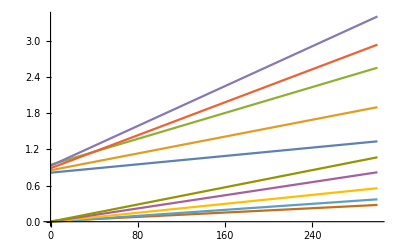

```mathematica
Plot[{Evaluate@Normal[falinelist],Evaluate@Normal[thermalfalinelist]},{x,0,300}]
```

```mathematica
SlopeExtractor@falinelist/(SlopeExtractor@thermalfalinelist)
```

{1.9228,2.7975,2.90053,2.50523,2.31934}

```mathematica
SlopeExtractor@templinelist/(SlopeExtractor@thermaltemplinelist)
```

{1.88663,1.74823,1.60644,1.3935,1.21255}

```mathematica
Transpose[Partition[SlopeExtractor/@ToExpression/@Names["`*line*"],4]]
```

{{{0.0017342,0.00349061,0.0053665,0.00683359,0.00825702},{0.000901913,0.00124776,0.00185018,0.00272773,0.00356008}},{{0.00425163,0.00349061,0.00282867,0.00215914,0.00205877},{0.00220411,0.00178176,0.00159293,0.000870688}},{{0.00425163,0.00349061,0.00282867,0.00215914,0.00205877},{0.00257308,0.00211976,0.00193966,0.00137671,0.00186095}},{{0.00349061,0.00542588,0.00800132,0.0114741,0.0151478},{0.00185018,0.00310365,0.00498078,0.00823401,0.0124926}}}

```mathematica
F/R /(273.15+{25,30,35,40,45})*SlopeExtractor@thermaltemplinelist
```

{0.00185018,0.00305246,0.00481915,0.00783959,0.0117072}

```mathematica
SlopeExtractor@templinelist
```

{-0.00349061,-0.00542588,-0.00800132,-0.0114741,-0.0151478}

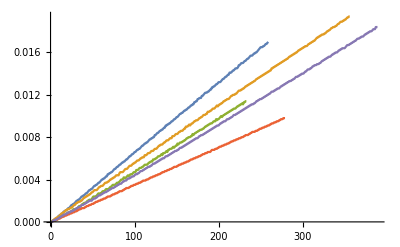

```mathematica
ListLinePlot[thermalkbrrawlist]
```

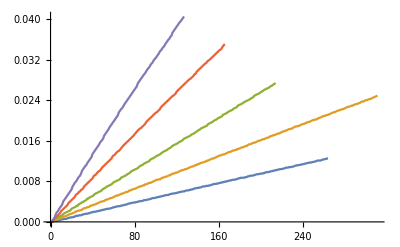

```mathematica
ListLinePlot[thermaltemprawlist]
```

```mathematica
Import[#,"Table"]&/@FileNames["*.txt"]
```

{{{0.6,1},{0.6,2},{0.7,3},{0.7,4},{0.8,5},{0.7,6},{0.8,7},303,{18.1,311},{18.2,312},{18.2,313},{18.3,314},{18.3,315},{18.4,316},{18.4,317}},17,{1}}
 |  |  |  |

```mathematica
thermalhclrawlist=FileNames["*.txt"][[{1,2,3,-1}]];
thermalkbrrawlist=FileNames["*.txt"][[{8,9,5,6,7}]];
thermalfarawlist=FileNames["*.txt"][[{11,12,13,14,10}]];
thermaltemprawlist=FileNames["*.txt"][[{-7,-5,-4,-3,-2}]];
```

```mathematica
RangeSelector[data_]:=Manipulate[ListLinePlot[data[[i;;j]]],{i,1,j,1},{j,1,Length[data],1}];
```

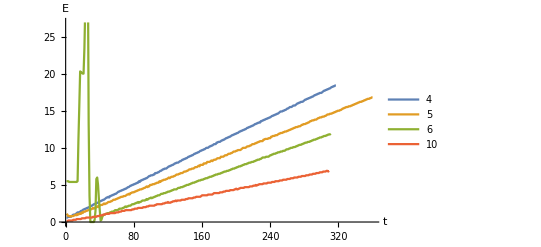

```mathematica
ListLinePlot[First/@Import[#,"Table"]&/@thermalhclrawlist,PlotLegends->{"4","5","6","10"},AxesLabel->{"t","E"}]
```

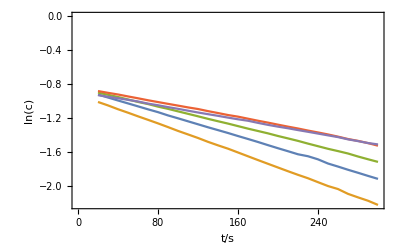

```mathematica
ListLinePlot[Map[{#[[1]],Log[#[[2]]]}&[Drop[Drop[#,-4],1]]&,Drop[First@Import[#],15]&/@hclrawlist,{2}],Frame->True,Axes->False,FrameLabel->{"t/s","ln(c)"}]
```

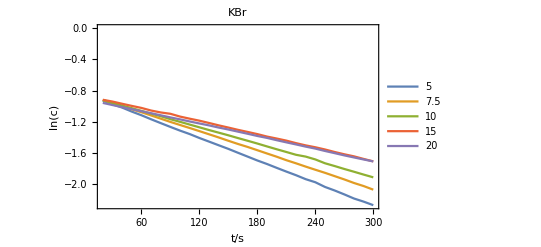

```mathematica
ListLinePlot[Map[{#[[1]],Log[#[[2]]]}&[Drop[Drop[#,-4],1]]&,Drop[First@Import[#],15]&/@kbrrawlist,{2}],Frame->True,Axes->False,FrameLabel->{"t/s","ln(c)"},PlotRange->All,PlotLabel->"KBr",PlotLegends->{"5","7.5","10","15","20"}]
```

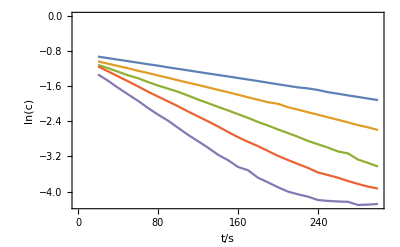

```mathematica
ListLinePlot[Map[{#[[1]],Log[#[[2]]]}&[Drop[Drop[#,-4],1]]&,Drop[First@Import[#],15]&/@temprawlist,{2}],Frame->True,Axes->False,FrameLabel->{"t/s","ln(c)"}]
```

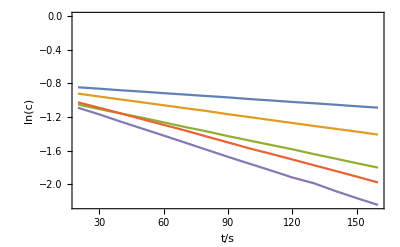

```mathematica
ListLinePlot[Take[#,15]&/@falist,Frame->True,Axes->False,FrameLabel->{"t/s","ln(c)"},PlotRange->All]
```

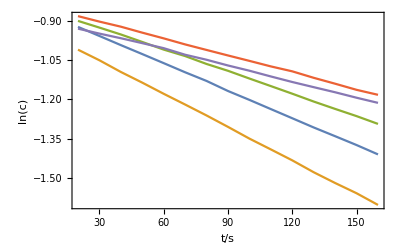

```mathematica
ListLinePlot[Take[#,15]&/@hcllist,Frame->True,Axes->False,FrameLabel->{"t/s","ln(c)"},PlotRange->All]
```

```mathematica
#["RSquared"]&/@templinelist
```

{0.999963,0.999928,0.999431,0.999916,0.999844}

```mathematica
#["RSquared"]&/@hcllinelist
```

{0.999963,0.999948,0.999774,0.99979,0.999584}

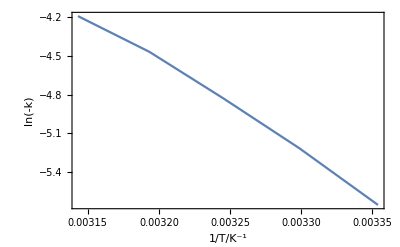

```mathematica
ListLinePlot[Transpose[{1/({25,30,35,40,45}+273.15),Log[-Last/@(#["BestFitParameters"]&/@templinelist)]}],Frame->True,Axes->False,FrameLabel->{"1/T/K^-1","ln(-k)"}]
```

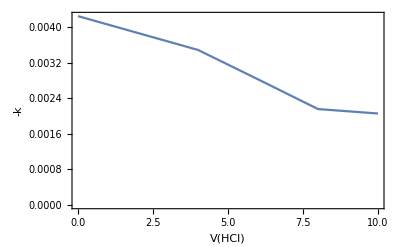

```mathematica
ListLinePlot[Transpose[{{0,4,6,8,10},-Last/@(#["BestFitParameters"]&/@hcllinelist)}],Frame->True,Axes->False,FrameLabel->{"V(HCl)","-k"}]
```

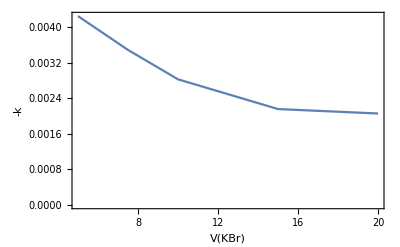

```mathematica
ListLinePlot[Transpose[{{5,7.5,10,15,20},-Last/@(#["BestFitParameters"]&/@kbrlinelist)}],Frame->True,Axes->False,FrameLabel->{"V(KBr)","-k"}]
```

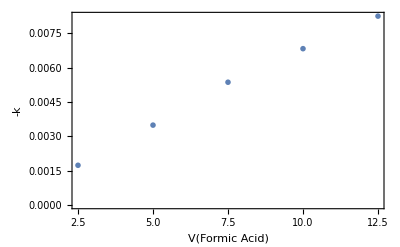

```mathematica
ListPlot[Transpose[{{2.5,5,7.5,10,12.5},-Last/@(#["BestFitParameters"]&/@falinelist)}],Frame->True,Axes->False,FrameLabel->{"V(Formic Acid)","-k"},PlotStyle->PointSize[0.01]]
```

```mathematica
LinearModelFit[Transpose[{{0,4,6,8,10},Log[-Last/@(#["BestFitParameters"]&/@hcllinelist)]}],{1,a},a]["RSquared"]
```

0.996029

```mathematica
FindFit[Transpose[{{2.5,5,7.5,10,12.5},-Last/@(#["BestFitParameters"]&/@kbrlinelist)}],a/(b x +1),{a,b},x]
```

{a→0.00599335,b→0.156229}

```mathematica
NonlinearModelFit[Transpose[{{2.5,5,7.5,10,12.5},-Last/@(#["BestFitParameters"]&/@kbrlinelist)}],a/(b x +1),{a,b},x]["RSquared"]
```

0.998787

```mathematica
Mediator[interval_,step_]:=Integrate[Exp[-t],{t,#1,#2}]&@@@Transpose[{Table[i,{i,1,interval,step}],step+Table[i,{i,1,interval,step}]}];ConvolutedMediator[interval_,step_]:=Integrate[Exp[-t]*t-#1,{t,#1,#2}]&@@@Transpose[{Table[i,{i,1,interval,step}],step+Table[i,{i,1,interval,step}]}];
```

```mathematica
Table[LinearModelFit[Transpose[{Mean/@Transpose[{Table[i,{i,1,100,i}],i+Table[i,{i,1,100,i}]}],Log[Mediator[100,i]]}],{1,x},x]["BestFitParameters"],{i,0.1,1,0.1}]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Cosh[541/10]-Cosh[271/5]-Sinh[541/10]+Sinh[271/5].

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Cosh[271/5]-Cosh[543/10]-Sinh[271/5]+Sinh[543/10].

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Cosh[543/10]-Cosh[272/5]-Sinh[543/10]+Sinh[272/5].

General::stop: Further output of N::meprec will be suppressed during this calculation.

{{-2.30217,-1.},{-1.60777,-1.},{-1.20023,-1.},{-0.909633,-1.},{-0.682752,-1.},{-0.49587,-1.},{-0.336341,-1.},{-0.196618,-1.},{-0.0718354,-1.},{0.0413249,-1.}}

```mathematica
Table[LinearModelFit[Transpose[{Mean/@Transpose[{Table[i,{i,1,100,i}],i+Table[i,{i,1,100,i}]}],Log[ConvolutedMediator[100,i]]}],{1,x},x]["BestFitParameters"],{i,0.1,1,0.1}]//Quiet
Table[LinearModelFit[Transpose[{Mean/@Transpose[{Table[i,{i,1,100,i}],i+Table[i,{i,1,100,i}]}],Log[ConvolutedMediator[100,i]]}],{1,x},x]["RSquared"],{i,0.1,1,0.1}]//Quiet
```

{LinearModelFit[{{1.05,-2.76034+3.14159 ⅈ},{1.15,-2.60914+3.14159 ⅈ},{1.25,-2.47461+3.14159 ⅈ},986,{99.95,2.30158+3.14159 ⅈ},{100.05,2.30259+3.14159 ⅈ}},{1,x},x][BestFitParameters],8,LinearModelFit[1][BestFitParameters]}
 |  |  |  |

{LinearModelFit[{{1.05,-2.76034+3.14159 ⅈ},{1.15,-2.60914+3.14159 ⅈ},{1.25,-2.47461+3.14159 ⅈ},986,{99.95,2.30158+3.14159 ⅈ},{100.05,2.30259+3.14159 ⅈ}},{1,x},x][RSquared],8,LinearModelFit[{1},{1,x},x][RSquared]}
 |  |  |  |

```mathematica
Table[LinearModelFit[Transpose[{Mean/@Transpose[{Table[i,{i,1,100,i}],i+Table[i,{i,1,100,i}]}],Log[Mediator[100,i]]}],{1,x},x]["RSquared"],{i,0.1,1,0.1}]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Cosh[541/10]-Cosh[271/5]-Sinh[541/10]+Sinh[271/5].

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Cosh[271/5]-Cosh[543/10]-Sinh[271/5]+Sinh[543/10].

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Cosh[543/10]-Cosh[272/5]-Sinh[543/10]+Sinh[272/5].

General::stop: Further output of N::meprec will be suppressed during this calculation.

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
LinearModelFit[Transpose[{1/(273.15+{25,30,35,40,45}),Log[SlopeExtractor@templinelist]}],{1,x},x]["RSquared"]
```

0.996029

```mathematica
LinearModelFit[Transpose[{1/(273.15+{25,30,35,40,45}),Log[SlopeExtractor@templinelist]}],{1,x},x]["BestFitParameters"]
```

{17.8541,-6999.34}

```mathematica
LinearModelFit[#,{1,t},t]&/@Log[Table[(Exp[-k t]-Exp[- t]) k /(1-k),{k,2,10},{t,1,10}]]
```

{FittedModel[0.442871-0.966937 t],FittedModel[0.340403-0.991203 t],FittedModel[0.266393-0.997105 t],FittedModel[0.215636-0.998977 t],FittedModel[0.179602-0.999629 t],FittedModel[0.153156-0.999864 t],FittedModel[0.133166-0.99995 t],FittedModel[0.117649-0.999982 t],FittedModel[0.105311-0.999993 t]}

```mathematica
hcoohc={{2.5,5,7.5,10,12.5},0.02{2.5,5,7.5,10,12.5}};
hclc={{4,5,6,8,10},0.02{4,5,6,8,10}};
kbrc={{5,7.5,10,15,20},0.01{5,7.5,10,15,20}};
thermalhcoohc={{1.5,2.5,3.5,5.0,7.5},0.02{1.5,2.5,3.5,5.0,7.5}};
thermalhclc={{4,5,6,10},0.02{4,5,6,10}};
thermalkbrc={{5,6,10,15},0.02{5,6,10,15}};
```

```mathematica
Transpose[{hclc[[2]],SlopeExtractor@hcllinelist,#["RSquared"]&/@hcllinelist}]//Transpose//TableForm//TeXForm
```

\begin{array}{ccccc}
 0.08 & 0.1 & 0.12 & 0.16 & 0.2 \\
 0.00425163 & 0.00349061 & 0.00282867 & 0.00215914 &
   0.00205877 \\
 0.999948 & 0.999963 & 0.999774 & 0.99979 & 0.999584
   \\
\end{array}

```mathematica
Transpose[{kbrc[[2]],1000*SlopeExtractor@kbrlinelist}]~SetPrecision~4//Transpose//TableForm//TeXForm
```

\begin{array}{ccccc}
 0.05000 & 0.07500 & 0.1000 & 0.1500 & 0.2000 \\
 4.803 & 4.035 & 3.491 & 2.760 & 2.626 \\
\end{array}

```mathematica
Transpose[{hcoohc[[2]],1000*SlopeExtractor@templinelist}]~SetPrecision~4//Transpose//TableForm//TeXForm
```

\begin{array}{ccccc}
 0.05000 & 0.1000 & 0.1500 & 0.2000 & 0.2500 \\
 3.491 & 5.426 & 8.001 & 11.47 & 15.15 \\
\end{array}

```mathematica
LinearModelFit[kbrc,{1,x},x]["RSquared"]
```

LinearModelFit::fitc: Number of coordinates (4) is not equal to the number of variables (1).

LinearModelFit[{{5,7.5,10,15,20},{0.05,0.075,0.1,0.15,0.2}},{1,x},x][RSquared]

```mathematica
{#["RSquared"]&/@templinelist}~SetPrecision~6//TableForm//TeXForm
```

\begin{array}{ccccc}
 0.999963 & 0.999928 & 0.999431 & 0.999916 &
   0.999844 \\
\end{array}

```mathematica
Transpose[{thermalhcoohc[[2]]~SetPrecision~4,1000*SlopeExtractor@thermalfalinelist~SetPrecision~4,(#["RSquared"]&/@thermalfalinelist)~SetPrecision~6}]//Transpose//TableForm//TeXForm
```

\begin{array}{ccccc}
 0.03000 & 0.05000 & 0.07000 & 0.1000 & 0.1500 \\
 0.9019 & 1.248 & 1.850 & 2.728 & 3.560 \\
 0.999886 & 0.999846 & 0.999843 & 0.999938 &
   0.999907 \\
\end{array}

```mathematica
Transpose[{1000*SlopeExtractor@thermaltemplinelist~SetPrecision~4,(#["RSquared"]&/@thermaltemplinelist)~SetPrecision~6}]//Transpose//TableForm//TeXForm
```

```mathematica
SlopeExtractor@thermalkbrlinelist
```

{0.00257308,0.00211976,0.00193966,0.00137671,0.00186095}

```mathematica
Export["hcooh.eps",Function[{dataset1,dataset2},Show[GraphFormatize[ListPlot[{Transpose[dataset1],
Transpose[dataset2]}
,Frame->True,Axes->False,FrameLabel->MaTeX/@{"c(\\text{HCOOH})","k/\mathrm{s}"},PlotStyle->Thick,PlotMarkers->Automatic,PlotLegends->TimesNewRoman/@{"A","B"}]],
Plot[Evaluate[{Normal[LinearModelFit[Transpose@dataset1,{1,x},x]],Normal[LinearModelFit[Transpose@dataset2,{1,x},x]]}],{x,0,0.25},PlotStyle->{Default,Dashed}]]]@@{{hcoohc[[2]],SlopeExtractor@falinelist},{thermalhcoohc[[2]],SlopeExtractor@thermalfalinelist}}]
```

OptionValue::nodef: Unknown option PlotStyle for Graphics.

hcooh.eps

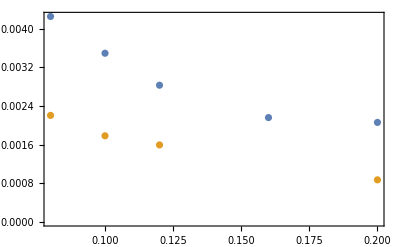

```mathematica
ListPlot[{Transpose[{hclc[[2]],Last/@(#["BestFitParameters"]&/@hcllinelist)}],
Transpose@{thermalhclc[[2]],Last/@(#["BestFitParameters"]&/@thermalhcllinelist)}}
,Frame->True,Axes->False,FrameLabel->MaTeX/@{"c(\\text{HCl})","k/\mathrm{s}"},PlotStyle->Thick]
```

```mathematica
Export["hcl.eps",Function[{dataset1,dataset2},Show[GraphFormatize[ListPlot[{Transpose[dataset1],
Transpose[dataset2]}
,Frame->True,Axes->False,FrameLabel->MaTeX/@{"c(\\text{HCl})","k/\mathrm{s}"},PlotStyle->Thick,PlotMarkers->Automatic,PlotLegends->TimesNewRoman/@{"A","B"}]],
Plot[Evaluate[{Normal[NonlinearModelFit[Transpose@dataset1,{q/(1+s x)},{s,q},x]],Normal[NonlinearModelFit[Transpose@dataset2,{q/(1+s x)},{s,q},x]]}],{x,0,0.25},PlotStyle->{Default,Dashed}]]]@@{{hclc[[2]],SlopeExtractor@hcllinelist},{thermalhclc[[2]],SlopeExtractor@thermalhcllinelist}}]
```

OptionValue::nodef: Unknown option PlotStyle for Graphics.

hcl.eps

```mathematica
Export["kbr.eps",Function[{dataset1,dataset2},Show[GraphFormatize[ListPlot[{Transpose[dataset1],
Transpose[dataset2]}
,Frame->True,Axes->False,FrameLabel->MaTeX/@{"c(\\text{KBr})","k/\mathrm{s}"},PlotStyle->Thick,PlotMarkers->Automatic,PlotLegends->TimesNewRoman/@{"A","B"}]],
Plot[Evaluate[{Normal[NonlinearModelFit[Transpose@dataset1,{q/(1+s x)},{s,q},x]],Normal[NonlinearModelFit[Transpose@dataset2,{q/(1+s x)},{s,q},x]]}],{x,0,0.4},PlotStyle->{Default,Dashed}]]]@@{{kbrc[[2]],SlopeExtractor@kbrlinelist},{thermalkbrc[[2]],SlopeExtractor@thermalkbrlinelist}}]
```

OptionValue::nodef: Unknown option PlotStyle for Graphics.

kbr.eps

```mathematica
Export["exptemp.eps",Function[{dataset1,dataset2},Show[GraphFormatize[ListPlot[{Transpose[dataset1],
Transpose[dataset2]}
,Frame->True,Axes->False,FrameLabel->MaTeX/@{"1/(T/\\mathrm{K})","\\ln{(k/\mathrm{s})}"},PlotStyle->Thick,PlotMarkers->Automatic,PlotLegends->TimesNewRoman/@{"A","B"}]],
Plot[Evaluate[{Normal[LinearModelFit[Transpose@dataset1,{1,x},x]],Normal[LinearModelFit[Transpose@dataset2,{1,x},x]]}],{x,0,0.4},PlotStyle->{Default,Dashed}]]]@@{{1/(298.15+{0,5,10,15,20}),Log@SlopeExtractor@templinelist},{1/(298.15+{0,5,10,15,20}),Log@SlopeExtractor@thermaltemplinelist}}]
```

OptionValue::nodef: Unknown option PlotStyle for Graphics.

exptemp.eps

```mathematica
Function[{dataset1,dataset2},{Normal[NonlinearModelFit[Transpose@dataset1,{q/(1+s x)},{s,q},x]],Normal[NonlinearModelFit[Transpose@dataset2,{q/(1+s x)},{s,q},x]]}]@@{{kbrc[[2]],SlopeExtractor@kbrlinelist},{thermalkbrc[[2]],SlopeExtractor@thermalkbrlinelist}}
```

{0.00693094/(1+9.33714 x),0.00385937/(1+5.64876 x)}

```mathematica
Function[{dataset1,dataset2},{NonlinearModelFit[Transpose@dataset1,{q/(1+s x)},{s,q},x]//Normal,NonlinearModelFit[Transpose@dataset2,{q/(1+s x)},{s,q},x]}]@@{{hclc[[2]],SlopeExtractor@hcllinelist},{thermalhclc[[2]],SlopeExtractor@thermalhcllinelist}}
```

{0.0284047/(1+71.825 x),FittedModel[0.0303935/(1+158.798 x)]}

```mathematica
Function[{dataset1,dataset2},{NonlinearModelFit[Transpose@dataset1,{q/(1+s x)},{s,q},x]["RSquared"],NonlinearModelFit[Transpose@dataset2,{q/(1+s x)},{s,q},x]["RSquared"]}]@@{{kbrc[[2]],SlopeExtractor@kbrlinelist},{thermalkbrc[[2]],SlopeExtractor@thermalkbrlinelist}}
```

{0.998844,0.996225}

```mathematica
Function[{dataset1,dataset2},{LinearModelFit[Transpose@dataset1,{1,x},x]["RSquared"],LinearModelFit[Transpose@dataset2,{1,x},x]["RSquared"]}]@@{{hcoohc[[2]],SlopeExtractor@falinelist},{thermalhcoohc[[2]],SlopeExtractor@thermalfalinelist}}
```

{0.996417,0.985107}

```mathematica
Function[{dataset1,dataset2},{LinearModelFit[Transpose@dataset1,{1,x},x]["RSquared"],LinearModelFit[Transpose@dataset2,{1,x},x]["RSquared"]}]@@{{1/(298.15+{0,5,10,15,20}),Log@SlopeExtractor@templinelist},{1/(298.15+{0,5,10,15,20}),Log@SlopeExtractor@thermaltemplinelist}}
```

{0.996029,0.999577}